```mathematica
<<sddsInterpret`
```

This is an example multi-page tracking file.
We are going to read the parameters and variables in, but give them a prefix (sddsPrefix) and make them all capitals (for some reason, MakeCapitals).
Also we only choose page 2 and 3 - 3 doesn’t exist so it should ignore it!

```mathematica
sddsInterpret["F:\\mad\\CanScan\\modified\\14mm\\nominal.all.W1",sddsVerbose->True,sddsPrefix->"binary",MakeCapitals->True,ChoosePage->{2,3}]
```

sddsInterpret::badpages: Pages {3} are not less than or equal to number of pages. Returning valid pages.

Number of Pages: 2;	Current Page(s): {2}

Variables (Re)Assigned: {BINARYX, BINARYXP, BINARYY, BINARYYP, BINARYT, BINARYP, BINARYDT, BINARYPARTICLEID}

Parameters (Re)Assigned: {BINARYSTEP, BINARYPCENTRAL, BINARYCHARGE, BINARYPARTICLES, BINARYPASS, BINARYPASSLENGTH, BINARYPASSCENTRALTIME, BINARYELAPSEDTIME, BINARYELAPSEDCORETIME, BINARYS, BINARYDESCRIPTION, BINARYPREVIOUSELEMENTNAME, BINARYFILENAME, BINARYNUMBERCOMBINED}

```mathematica
Dimensions[BINARYX]
```

{1,2000}

This is the same file but converted to ASCII, and we read in all pages

```mathematica
sddsInterpret["F:\\mad\\CanScan\\modified\\14mm\\nominal.all.ascii.W1",sddsVerbose->True]
```

Number of Pages: 2;	Current Page(s): {1, 2}

Variables (Re)Assigned: {x, xp, y, yp, t, p, dt, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, Pass, PassLength, PassCentralTime, ElapsedTime, ElapsedCoreTime, s, Description, PreviousElementName, Filename, NumberCombined}

Just to prove that we read in the correct pages:

```mathematica
Dimensions[x]
```

{2,2000}

```mathematica
BINARYX==x[[{1}]]
```

False

```mathematica
BINARYX==x[[{2}]]
```

True

Can now plot the variables - note that they are in arrays, since this is a multi-page file:

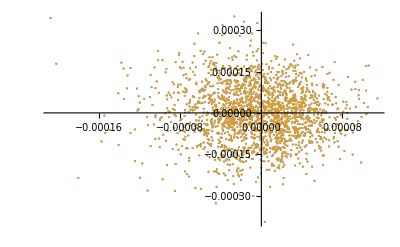

```mathematica
ListPlot[{Transpose[{BINARYX[[1]],y[[2]]}],Transpose[{x[[2]],BINARYY[[1]]}]}]
```

This is a single page binary file:

```mathematica
sddsInterpret["F:\\mad\\CanScan\\modified\\14mm\\nominal-001.W1",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {x, xp, y, yp, t, p, dt, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, Pass, PassLength, PassCentralTime, ElapsedTime, ElapsedCoreTime, s}

Parameters are now in lists to make things a little easier...

```mathematica
Dimensions[x]
```

{2000}

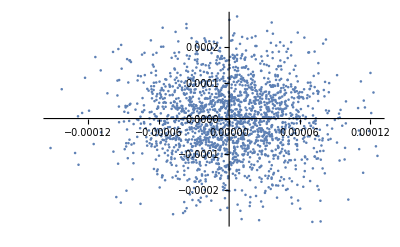

```mathematica
ListPlot[{Transpose[{x,y}]}]
```